# Übung 1

```mathematica
ClearAll["Global`*"]
```

## Data

```mathematica
ydata={11,89,65,71,48,28,16,6,2};
xdata=Range[0,8];
data=Transpose[{xdata,ydata}];
```

```mathematica
wData=WeightedData[xdata,ydata]
```

WeightedData[…]

```mathematica
μ=(xdata.ydata)/Total[ydata]//N
```

2.73214

```mathematica
Sqrt[((xdata-μ)^2).ydata/Total[ydata]]
```

1.67784

## Plotting

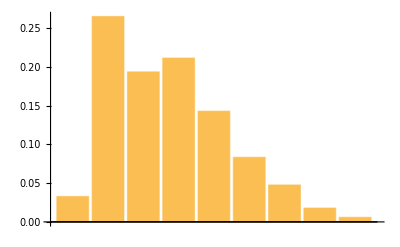

```mathematica
BarChart[ydata/Total[ydata]]
```

```mathematica
PoissonDistribution[μ]
```

PoissonDistribution[2.73214]

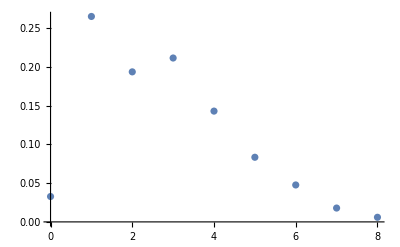

```mathematica
ListPlot[Transpose[{xdata,ydata/Total[ydata]}]]
```

```mathematica
Total[ydata]
```

336

```mathematica
{1,2}.{10,9}
```

28

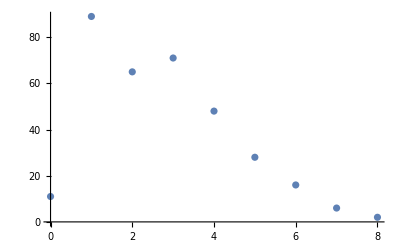

```mathematica
ListPlot[data]
```

## PDF

```mathematica
dist=PoissonDistribution[μ]
```

PoissonDistribution[2.73214]

```mathematica
Table[PDF[dist][x],{x,0,8}]
```

{0.0650797,0.177807,0.242897,0.22121,0.151094,0.0825622,0.0375953,0.0146737,0.00501132}

```mathematica
expData={Range[0,8],ydata,N[ydata/Total[ydata],5],N[Table[PDF[dist][x],{x,0,8}],5]};
```

```mathematica
expData
```

{{0,1,2,3,4,5,6,7,8},{11,89,65,71,48,28,16,6,2},{0.032738,0.26488,0.19345,0.21131,0.14286,0.083333,0.047619,0.017857,0.0059524},{0.0650797,0.177807,0.242897,0.22121,0.151094,0.0825622,0.0375953,0.0146737,0.00501132}}

```mathematica
TeXForm[expData]//CopyToClipboard
```

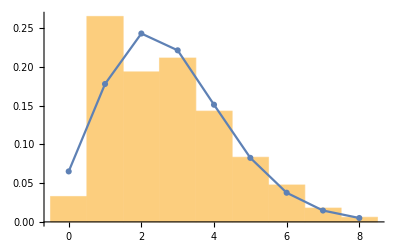

```mathematica
Show[Histogram[wData,9,"Probability"],ListPlot[Table[{x,PDF[dist][x]},{x,0,8}],Joined->True,PlotMarkers->Automatic]]
```

```mathematica
Export[NotebookDirectory[]<>"fig1.pdf",Show[Histogram[wData,9,"Probability"],ListPlot[Table[{x,PDF[dist][x]},{x,0,8}],Joined->True,PlotMarkers->Automatic],ImageSize->Large,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[20,Black],FrameLabel->{"Ereignis","Relative Häufigkeit"},LabelStyle->Directive[Black,20]],Background->None];
```